# Axions in NS plots

## Dependencies and Globals

```mathematica
(* LOAD PACKAGES *)
Needs["MaTeX`"];
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts,xcolor}"}];

(* PRECISION AND ACCURACY *)
NPRECISON = 13;

(* GLOBALS *)
Msun=1.989*10^30;(* kg *)
GN = 6.67*10^-11; (* SI *)
G=(*6.70883*10^(-57)*)1; (* eV^-2 *)
clight = 2.99792458*10^8; (* m/s *)
eV2joules=1.60218*10^(-19);
GeV2joules=1.60218*10^(-10);
mN = 0.939563; (* GeV *)
hbarGeV=6.582119569*10^(-25); (* GeV S *)
hbarJ = 1.05457*10^(-34); (* J s *)
hbarGeo = hbarJ * (GN / clight^4) * clight; (* m^2 *)
(*GNeV = 6.70883*10^(-39);*)
σN = 0.059;(* GeV *)(* eV*s *)
rkm=10^3 / (hbarGeV*clight);
rm=1/(hbarGeV*clight);
mpi = 0.134977;
fpi = 0.130;

MeVperfm3 2 Jperm3=(10^-3*GeV2joules) * (10^(-15))^(-3);
Jperm3 2 m2 = GN / clight^4;
GeV2m = GeV2joules*GN/clight^4;

RescaleMRPair km Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]]/10^3, ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRΛTriplet km Msun dim0[MRΛTriplet_,scales_]:={(MRΛTriplet[[1]])*scales[[1]]/10^3, ((MRΛTriplet[[2]])*scales[[3]]*clight^2/GN)/Msun,MRΛTriplet[[3]]}
RescaleMRPair m Msun[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]])*scales[[3]]*clight^2/GN)/Msun}
RescaleMRPair m kg[MRPair_,scales_]:={(MRPair[[1]])*scales[[1]], ((MRPair[[2]]*clight^2/GN)*scales[[1]]^3 * scales[[2]])}
RescaleM kg[mass_,scales_]:=((mass*clight^2/GN)*scales[[1]]^3 * scales[[2]])
RescaleR m[radius_,scales_]:=(radius)*scales[[1]]

TOV replacements={λ'[r]->D[Log[1/(1 - 2*M[r]/r)],r],λ''[r]->D[-Exp[λ[r]]*(2*M[r]/r^2 - 8*Pi*r*ρ[r]),r],
Exp[λ[r]]->1/(1 - 2*M[r]/r),
Exp[-λ[r]]->(1 - 2*M[r]/r),
λ[r]->Log[1/(1 - 2*M[r]/r)],Derivative[1][p][r]->-(((M[r]+4*Pi*r^3*p[r])*(p[r]+ρ[r]))/(r*(r-2*M[r]))),
Derivative[2][p][r]->Simplify[D[-(((M[r]+4*Pi*r^3*p[r])*(p[r]+ρ[r]))/(r*(r-2*M[r]))),r]],
Derivative[1][ν][r]->-2*(Derivative[1][p][r])/(p[r]+ρ[r]),
M'[r]->4*Pi*r^2*ρ[r]};

c1=RGBColor[101/255,144/255,255/255];
c2=RGBColor[121/255,94/255,240/255];
c3=RGBColor[221/255,38/255,129/255];
c4=RGBColor[255/255,97/255,2/255];
c5=RGBColor[254/255,176/255,1/255];
c6=RGBColor[200/255,200/255,200/255];
```

## Make data

```mathematica
MRPATH="/Users/wentmich/Documents/uiuc/research/axions-in-NS/run-outputs/debora-EOS-1-runs/";
files=FileNames["*.csv",MRPATH];
```

```mathematica
(* load in files that have perturbative axion params *)
ϵlimit = 0.1;
totaldata = {};
Module[{i,tempfile,matemp,fatemp},For[i=1,i<=Dimensions[files][[1]],i++,
tempfile=Import[files[[i]],"CSV"];
matemp=ToExpression[tempfile[[1]][[7]]];
fatemp=ToExpression[tempfile[[1]][[8]]];
If[4*fatemp^2*matemp^2/(fpi^2*mpi^2)<=ϵlimit,AppendTo[totaldata,tempfile],Print["not perturbative"]]]];
Print["Number of non-perturbative files: ", Dimensions[files][[1]] - Dimensions[totaldata][[1]]]
```

not perturbative

not perturbative

not perturbative

«4 more identical outputs»

Number of non-perturbative files: 7

```mathematica
madata = Table[ToExpression[totaldata[[i]][[1,7]]],{i,1,Dimensions[totaldata][[1]]}];
fadata = Table[totaldata[[i]][[1,8]],{i,1,Dimensions[totaldata][[1]]}];
```

```mathematica
MRdata = Table[{totaldata[[i]][[j,2]]/10^3,totaldata[[i]][[j,3]]*clight^2/GN/Msun},{i,1,Dimensions[totaldata][[1]]},{j,1,Dimensions[totaldata][[2]]}];
MaRdata = Table[{totaldata[[i]][[j,2]]/10^3,totaldata[[i]][[j,4]]*clight^2/GN/Msun},{i,1,Dimensions[totaldata][[1]]},{j,1,Dimensions[totaldata][[2]]}];
MtRdata =Table[{totaldata[[i]][[j,2]]/10^3,(totaldata[[i]][[j,3]]+totaldata[[i]][[j,4]])*clight^2/GN/Msun},{i,1,Dimensions[totaldata][[1]]},{j,1,Dimensions[totaldata][[2]]}];
ΛMdata = Table[{totaldata[[i]][[j,3]]*clight^2/GN/Msun,totaldata[[i]][[j,5]]},{i,1,Dimensions[totaldata][[1]]},{j,1,Dimensions[totaldata][[2]]}];
ΛtMtdata =Table[{(totaldata[[i]][[j,3]]+totaldata[[i]][[j,4]])*clight^2/GN/Msun,totaldata[[i]][[j,6]]},{i,1,Dimensions[totaldata][[1]]},{j,1,Dimensions[totaldata][[2]]}];
ΛCdata = Table[{totaldata[[i]][[j,3]]/totaldata[[i]][[j,2]],totaldata[[i]][[j,5]]},{i,1,Dimensions[totaldata][[1]]},{j,1,Dimensions[totaldata][[2]]}];
ΛtCtdata = Table[{(totaldata[[i]][[j,3]]+totaldata[[i]][[j,4]])/totaldata[[i]][[j,2]],totaldata[[i]][[j,6]]},{i,1,Dimensions[totaldata][[1]]},{j,1,Dimensions[totaldata][[2]]}];
```

## Plots

### MR Plot

```mathematica
ScientificForm[madata[[1]],2]
```

1/100000000000000000000000

```mathematica
mag = 1.0;
legenddata = Table[MaTeX[StringJoin["\\color{darkgray}m_a = ",ToString[ToString[madata[[i]],FortranForm]], ", f_a = ", ToString[ToString[TeXForm[ScientificForm[fadata[[i]]]]]]],Magnification->mag],{i,1,Dimensions[totaldata][[1]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MRfncs = {};
MtRfncs = {};
Module[{fnc,fnca,k},For[k=1,k<=Dimensions[totaldata][[1]],k++,
fnc=Interpolation[MRdata[[k]]];
fnca=Interpolation[MtRdata[[k]]];
AppendTo[MRfncs,fnc];
AppendTo[MtRfncs,fnca]]]
```

```mathematica
MRdiffvals lots = {};
For[k=1,k<=Dimensions[totaldata][[1]],k++,
AppendTo[MRdiffvals lots,Table[{M,1 -MtRfncs[[k]][M]/MRfncs[[k]][M]},{M,Max[{Min[MRdata[[k]][[All,1]]],Min[MtRdata[[k]][[All,1]]]}],Min[{Max[MtRdata[[k]][[All,1]]],Max[MRdata[[k]][[All,1]]]}],0.001}]]];
```

```mathematica
Dimensions[MRdiffvals lots]
```

{12}

```mathematica
MRdiffplot = ListPlot[MRdiffvals lots,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}C \\ \\left[\\text{a.u.} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Delta \\Lambda/\\Lambda_{a = 0}",Magnification->2.3]},PlotStyle->{{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick}},Joined->True,ImageSize->{700,200},PlotRange->{{12.5,15.0},All},AspectRatio->Full];
```

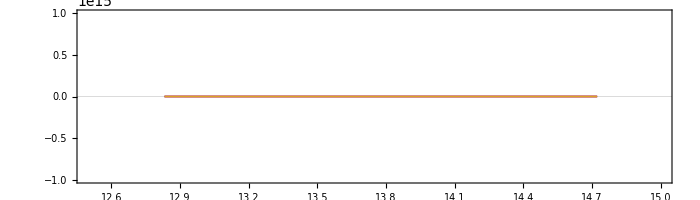

```mathematica
MRdiffplot
```

```mathematica
MRplot = ListPlot[Join[{MRdata[[1]]},MtRdata],PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}R_s \\ \\left[ \\text{km} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}M \\ \\left[M_{\\odot} \\right]",Magnification->2.3]},PlotStyle->{{c6,Thick,Dashed},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick}},Joined->{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},ImageSize->{800,500},PlotRange->{{12.5,15.0},{0.4,2.8}},PlotLegends->Placed[Join[{MaTeX["\\color{darkgray}a = 0",Magnification->mag]},legenddata], {0.8,0.8}]];
```

```mathematica
MRplot
```

-Graphics-

### ΛC Plot

```mathematica
mag = 1.0;
legenddata = Table[MaTeX[StringJoin["\\color{darkgray}m_a = ",ToString[ToString[madata[[i]],FortranForm]], ", f_a = ", ToString[ToString[TeXForm[ScientificForm[fadata[[i]]]]]]],Magnification->mag],{i,1,Dimensions[totaldata][[1]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
lambdaCfncs = {};
lambdatCtfncs = {};
Module[{fnc,fnca,k},For[k=1,k<=Dimensions[totaldata][[1]],k++,
fnc=Interpolation[ΛCdata[[k]]];
fnca=Interpolation[ΛtCtdata[[k]]];
AppendTo[lambdaCfncs,fnc];
AppendTo[lambdatCtfncs,fnca]]]
```

```mathematica
lambdaCdiffvals lots = {};
For[k=1,k<=Dimensions[totaldata][[1]],k++,
AppendTo[lambdaCdiffvals lots,Table[{M,1 -lambdatCtfncs[[k]][M]/lambdaCfncs[[k]][M]},{M,Max[{Min[ΛCdata[[k]][[All,1]]],Min[ΛtCtdata[[k]][[All,1]]]}],Min[{Max[ΛtCtdata[[k]][[All,1]]],Max[ΛCdata[[k]][[All,1]]]}],0.001}]]];
```

```mathematica
Dimensions[lambdaCdiffvals lots]
```

{12}

```mathematica
ΛCdiffplot = ListPlot[lambdaCdiffvals lots,PlotTheme->"Scientific",FrameLabel->{MaTeX["\\color{darkgray}C \\ \\left[\\text{a.u.} \\right]",Magnification->2.3],MaTeX["\\color{darkgray}\\Delta \\Lambda/\\Lambda_{a = 0}",Magnification->2.3]},PlotStyle->{{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick}},Joined->True,ImageSize->{700,200},PlotRange->{{0.04,0.33},All},AspectRatio->Full];
```

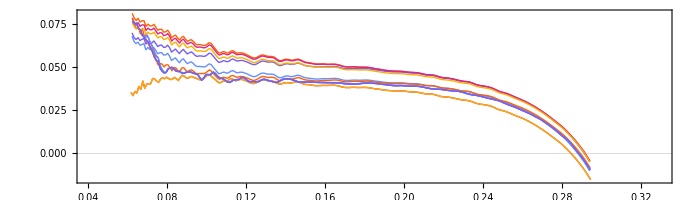

```mathematica
ΛCdiffplot
```

```mathematica
ΛCplot = ListLogPlot[Join[{ΛCdata[[1]]},ΛtCtdata],PlotTheme->"Scientific",FrameLabel->{(*MaTeX["\\color{darkgray}C \\ \\left[ \\text{a.u.} \\right]",Magnification->2.3]*)None,MaTeX["\\color{darkgray}\\Lambda \\ \\left[ \\text{a.u.} \\right]",Magnification->2.3]},PlotStyle->{{c6,Thick,Dashed},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick},{c1,Thick},{c2,Thick},{c3,Thick},{c4,Thick},{c5,Thick}},Joined->{True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False},ImageSize->{700,500},PlotRange->{{0.04,0.33},{2,5*10^4}},FrameTicks->{Automatic,Automatic},PlotLegends->Placed[Join[{MaTeX["\\color{darkgray}a = 0",Magnification->mag]},legenddata], {0.8,0.8}]];
```

```mathematica
ΛCplot
```

-Graphics-

```mathematica
GraphicsColumn[{ΛCplot,ΛCdiffplot}]
```

-Graphics-